# Modular Potential

# This notebook is a part of my Diploma Thesis with title “Swampland Conjectures and Constraints on Inflation” . The knowledge of the theoretical results is important, if someone wishes to follow the presented results in this notebook. My Thesis can be found in an other file in my GitHub repository.

## Definition of the Potential and Introduction of the Slow-Roll parameters

## In this section we will introduce the potential and the slow-roll parameters

```mathematica
v[x_]:=v0*(1-d*Exp[-l*k*x])
ε1=a/(2*k^2)*(v'[x]/v[x])^2// Simplify;
ε2=-a/k^2*(v''[x]/v[x])+ε1// Simplify;
ε=ε1/a// Simplify;
η=1/k^2*(v''[x]/v[x])// Simplify;
η1=a*η// Simplify;
```

(a d (-d+2 ⅇ^(k l x)) l^2)/(2 (d-ⅇ^(k l x))^2)

It is required by the theory that the period of inflation should stop when the flatness conditions are a not satisfied, so when ε1=1

```mathematica
Solve[ε1==1,x]
```

{{x→ConditionalExpression[(2 ⅈ π C[1]+Log[1/2 (2 d-√2 √a d l)])/(k l), C[1]∈ℤ]},{x→ConditionalExpression[(2 ⅈ π C[1]+Log[1/2 (2 d+√2 √a d l)])/(k l), C[1]∈ℤ]}}

We have to choose second possible solution, so we set with xf the final value for the φ.

```mathematica
xf=Log[1/2 (2 d+√2 √a d l)]/(k l)// Simplify;
```

We proceed to the calculation of the initial value of φ , which denoted as xi
Firstly, the integral for the e-folding number is calculated.

```mathematica
Integrate[(-k^2/a)*(v[x]/v'[x]),x]
```

(k (-ⅇ^(k l x)/(k l)+d x))/(a d l)

Then the xi is calculated. To avoid any problems in our code, e-folding number instead N will be noted as Y.

```mathematica
Solve[(k (-ⅇ^(k l xf)/(k l)))/(a d l)-(k (-ⅇ^(k l x)/(k l)))/(a d l)==Y,x]
```

{{x→ConditionalExpression[(2 ⅈ π C[1]+Log[1/2 d (2+√2 √a l+2 a l^2 Y)])/(k l), C[1]∈ℤ]}}

```mathematica
xi=Log[1/2 d (2+√2 √a l+2 a l^2 Y)]/(k l)// Simplify;
```

# Calculation of the observational indices

We calculate the slow-roll parameters for
φ = φi and we take the Taylor approximation for N → ∞. Afterwards, we
calculate the primordial density perturbation and the tensor to scalar ratio for φ = φi and we start our primary work.

```mathematica
ε1i=ε1/. x->xi;
Series[ε1i,{Y,Infinity,2}]
```

1/(2 a l^2 Y^2)+O[1/Y]^3

```mathematica
ε1i=1/(2 a l^2 Y^2);
```

```mathematica
ε2i=ε2/. x->xi;
Series[ε2i,{Y,Infinity,2}]
```

1/Y+(1-√2 √a l)/(2 a l^2 Y^2)+O[1/Y]^3

```mathematica
ε2i=1/Y+(1-√2 √a l)/(2 a l^2 Y^2)// Simplify
```

(1-√2 √a l)/(2 a l^2 Y^2)+1/Y

```mathematica
εi=ε/. x->xi// Simplify;
Series[εi,{Y,Infinity,2}]
```

1/(2 a^2 l^2 Y^2)+O[1/Y]^3

```mathematica
εi=1/(2 a^2 l^2 Y^2)
```

1/(2 a^2 l^2 Y^2)

```mathematica
ηi=η/. x->xi// Simplify;
Series[ηi,{Y,Infinity,2}]
```

-1/(a Y)+1/(√2 a^(3/2) l Y^2)+O[1/Y]^3

```mathematica
ηi=-1/(a Y)+1/(√2 a^(3/2) l Y^2)
```

1/(√2 a^(3/2) l Y^2)-1/(a Y)

```mathematica
η1i=η1/. x->xi// Simplify;
Series[η1i,{Y,Infinity,2}]
```

-1/Y+1/(√2 √a l Y^2)+O[1/Y]^3

```mathematica
η1i=-1/Y+1/(√2 √a l Y^2)
```

1/(√2 √a l Y^2)-1/Y

The the slow-roll parameters have to calculated for Y=60

```mathematica
ε1i60=ε1i /. Y->60;
ε2i60=ε2i /. Y->60;
εi60=εi /. Y->60;
η1i60=η1i /. Y->60;
ηi60=ηi /. Y->60;
```

The primordial density perturbation and the tensor to scalar ratio is given as:

```mathematica
ns=1-6*ε1i+2*η1i;
r=16*ε1i;
```

The primordial density perturbation and the tensor to scalar ratio for Y=60

```mathematica
ns60=ns/.Y->60//Simplify;
r60=r/. Y->60// Simplify;
```

• The spectral index of scalar density perturbations was found ns =
0.9649 ± 0.0042 at 68% CL.
• The upper limit of r is r < 0.1, but the combination with the data
from BICEP2/Keck Array BK15 provides that r < 0.056.
So we work for the aforementioned constrains:

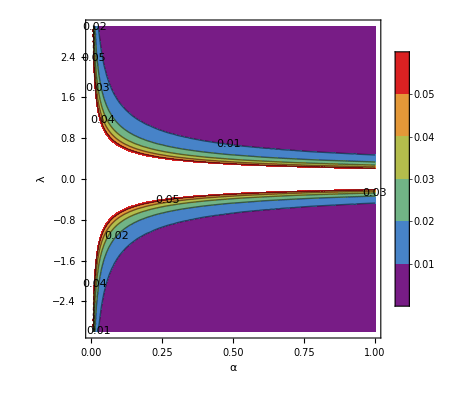

```mathematica
ContourPlot[r60,{a,0,1},{l,-3,3}, ContourLabels->True,ContourLabels->True,ColorFunction->"Rainbow",PlotLegends->Automatic, FrameLabel->{"α","λ"}, PlotRange->{0,0.056}]
```

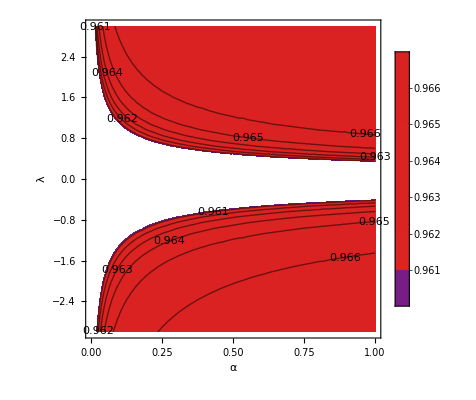

```mathematica
ContourPlot[ns60,{a,0,1},{l,-3,3},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"α","λ"}, ColorFunction->"Rainbow",PlotRange->{0.9607,0.9691}]
```

The slow-roll indices calculated with respect to the obtained constraints for λ<0

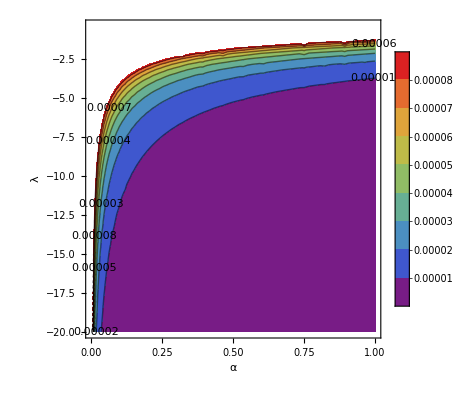

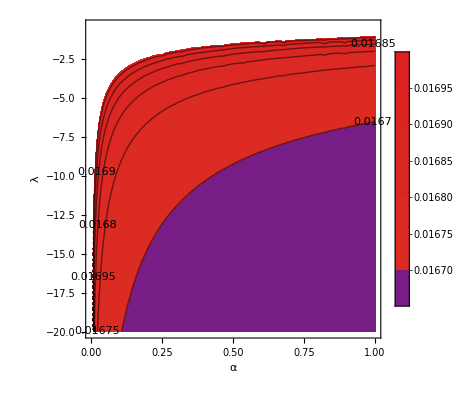

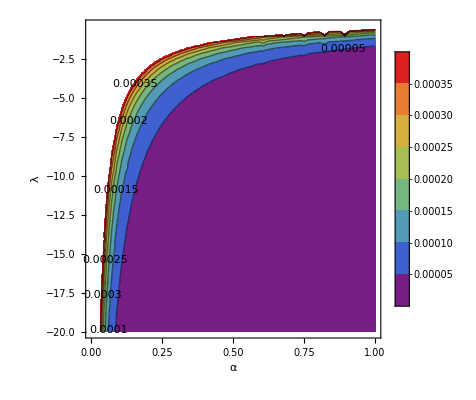

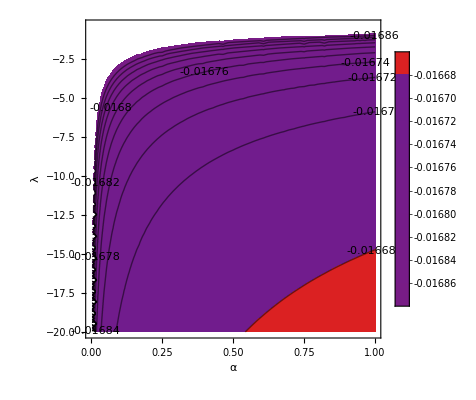

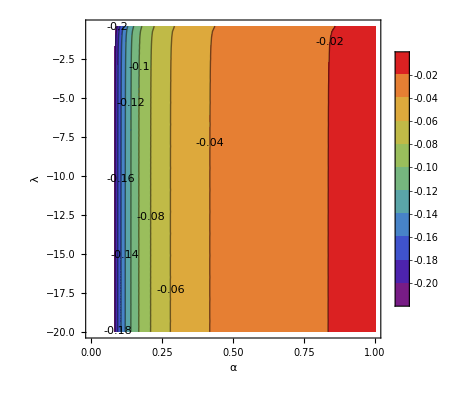

```mathematica
ContourPlot[ε1i60,{a,0,1},{l,-20,-0.408},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"α","λ"}, ColorFunction->"Rainbow"]
ContourPlot[ε2i60,{a,0,1},{l,-20,-0.408},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"α","λ"}, ColorFunction->"Rainbow"]
ContourPlot[εi60,{a,0,1},{l,-20,-0.408},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"α","λ"}, ColorFunction->"Rainbow"]
ContourPlot[η1i60,{a,0,1},{l,-20,-0.408},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"α","λ"}, ColorFunction->"Rainbow"]
ContourPlot[ηi60,{a,0,1},{l,-20,-0.408},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"α","λ"}, ColorFunction->"Rainbow"]
```

The slow-roll indices calculated with respect to the obtained constraints for λ>0

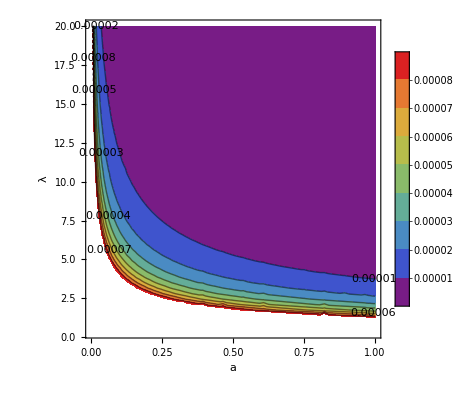

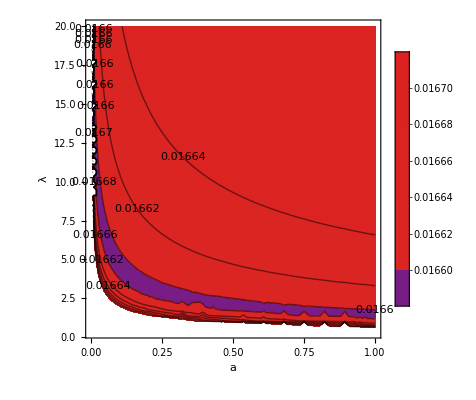

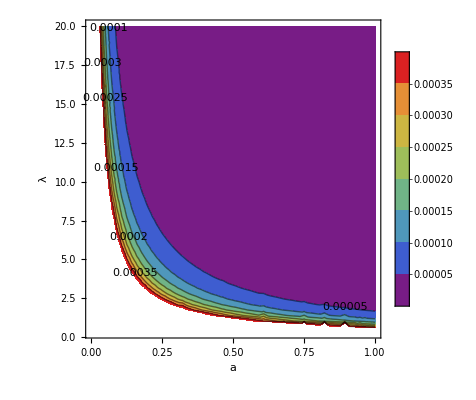

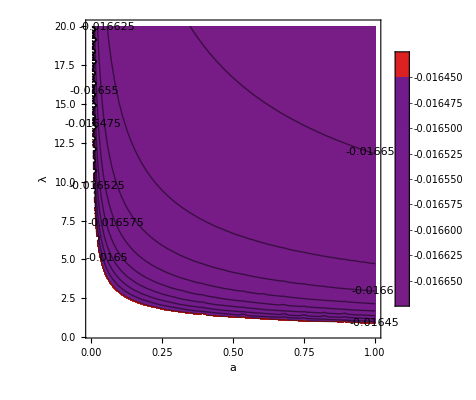

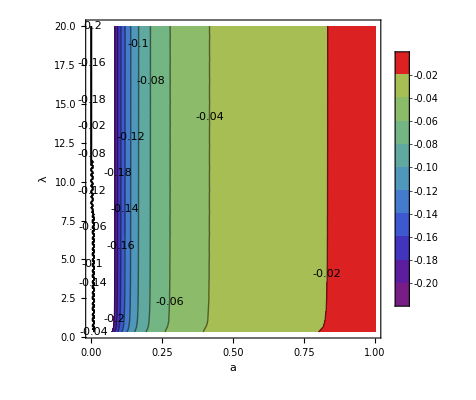

```mathematica
ContourPlot[ε1i60,{a,0,1},{l,0.342,20},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"a","λ"}, ColorFunction->"Rainbow"]
ContourPlot[ε2i60,{a,0,1},{l,0.342,20},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"a","λ"}, ColorFunction->"Rainbow"]
ContourPlot[εi60,{a,0,1},{l,0.342,20},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"a","λ"}, ColorFunction->"Rainbow"]
ContourPlot[η1i60,{a,0,1},{l,0.342,20},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"a","λ"}, ColorFunction->"Rainbow"]
ContourPlot[ηi60,{a,0,1},{l,0.342,20},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True,FrameLabel->{"a","λ"}, ColorFunction->"Rainbow"]
```

## Swampland Conjectures

• The Swampland Distance Conjecture limits the validity of an E.F.T.
and set an upper limit for the traversable by the scalar field as following

                                  ∆φ ≤ f ∼ O(1), in natural units

• The De Sitter Conjecture. It declares that it is impossible to create
De Sitter vacua in string theory. This leads us to set of a lower limit
for the gradient of scalar potentials [Tri20]:
V’/V≥ g ∼ O(1). 
• Another important result is the following -V”/V≥ g ∼ O(1).

```mathematica
s=-v''[x]/v[x];
si=s/. x->xi// Simplify;
si60=si/. Y->60// Simplify;
si60q=(2  l)/(√2 √a+120 a l)
```

(2 l)/(√2 √a+120 a l)

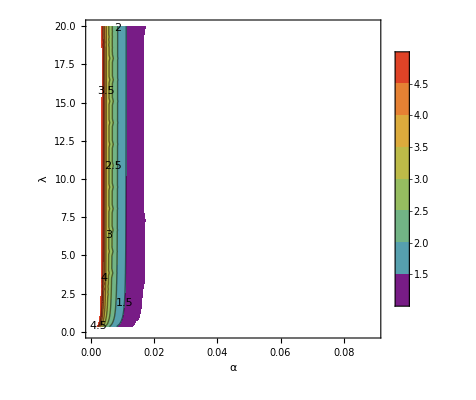

```mathematica
ContourPlot[si60q,{a,0.0015,0.09},{l,0.342,20},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True, ColorFunction->"Rainbow",FrameLabel->{"α","λ"},PlotRange->{1,5}]
```

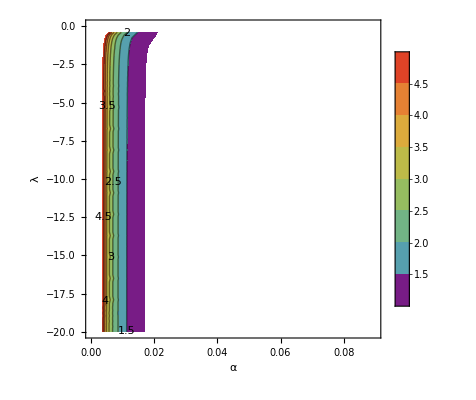

```mathematica
ContourPlot[si60q,{a,0.0015,0.09},{l,-20,-0.408},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True, ColorFunction->"Rainbow",FrameLabel->{"α","λ"},PlotRange->{1,5}]
```

```mathematica
w=v'[x]/v[x];

wi=w/. x->xi// Simplify;
wi60=2/(√2 √a+2 a l *60)// Simplify
```

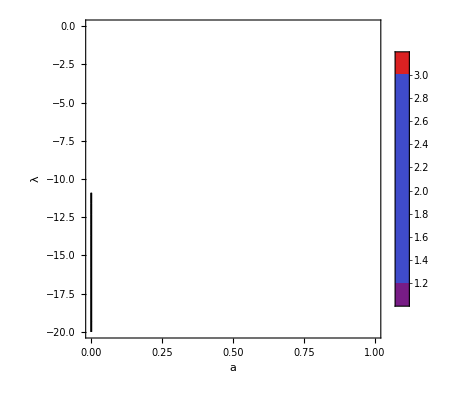

```mathematica
ContourPlot[wi60,{a,0,1},{l,-20,-0.408},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True, ColorFunction->"Rainbow",FrameLabel->{"a","λ"},PlotRange->{1,3}]
```

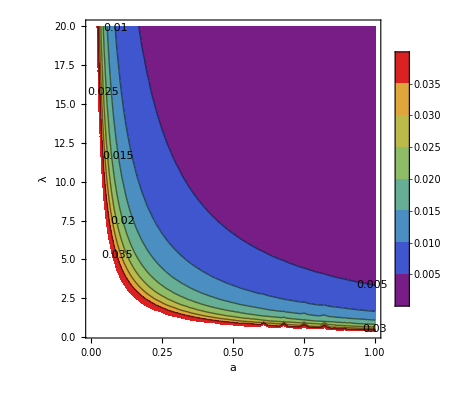

```mathematica
ContourPlot[wi60,{a,0,1},{l,0.342,20},PlotLegends->Automatic, AxesLabel->Automatic, ContourLabels->True, ColorFunction->"Rainbow",FrameLabel->{"a","λ"}]
```